# BlackHoleModelData

Get data about various black hole models

## Definition

```mathematica
BlackHoleModelData::pq="The input for `1` has incorrect units for `2`.";
BlackHoleModelData::indet="Unable to distinguish specific quantity variable for `1`.";
BlackHoleModelData::kerr="For these values no real event horizon exists and thus no black hole.";

$properties={"Coordinates","Entropy","HorizonArea","HorizonRadius","Metric","PenroseDiagram","SurfaceGravity","Temperature"};
$models={"Kerr","KerrNewman","ReissnerNordstrom","Schwarzschild"};
$pqnames={"M"->"mass","J"->"angular momentum","Q"->"electric charge","t"->"time","r"->"radial distance","θ"->"polar angle","ϕ"->"azimuth angle"};

(*data*)
(*"Kerr"|"KerrNewman"->"BoyerLindquist"*)
(*"Schwarzschild"|"ReissnerNordstrom"->"Schwarzschild"*)
blackholedata[_,"Coordinates"]={QuantityVariable["t","Time"],QuantityVariable["r","Radius"],QuantityVariable["θ","Angle"],QuantityVariable["ϕ","Angle"]};

(*metric helpers*)
alpha=QuantityVariable["J","AngularMomentum"]/(QuantityVariable["M","Mass"]*Quantity[1,"SpeedOfLight"]);
rho2=QuantityVariable["r","Radius"]^2+alpha^2 Cos[QuantityVariable["θ","Angle"]]^2;
rs=Quantity[2,"GravitationalConstant"/"SpeedOfLight"^2]*QuantityVariable["M","Mass"];
rq2=QuantityVariable["Q","ElectricCharge"]^2*Quantity[1,"GravitationalConstant"]/(4*Pi*Quantity[1,"ElectricConstant"]*Quantity[1,"SpeedOfLight"]^4);
delta=QuantityVariable["r","Radius"]^2-QuantityVariable["r","Radius"]*rs+alpha^2;
deltaQ=QuantityVariable["r","Radius"]^2+QuantityVariable["r","Radius"]*rs+alpha^2+rq2;
factor=QuantityVariable["M","Mass"]^2*Quantity[1,"SpeedOfLight"]^2;

modrho2=Simplify[rho2*factor];

blackholedata["Schwarzschild","Metric"]=Association[Subscript["G","tt"]->(1-rs/QuantityVariable["r","Radius"])*Quantity[1,"SpeedOfLight"]^2,Subscript["G","rr"]->(1-rs/QuantityVariable["r","Radius"])^(-1),Subscript["G","θθ"]->QuantityVariable["r","Radius"]^2,Subscript["G","ϕϕ"]->QuantityVariable["r","Radius"]^2*Sin[QuantityVariable["θ","Angle"]]^2];
blackholedata["ReissnerNordstrom","Metric"]=Association[Subscript["G","tt"]->(1-rs/QuantityVariable["r","Radius"]+rq2/QuantityVariable["r","Radius"]^2)*Quantity[1,"SpeedOfLight"]^2,Subscript["G","rr"]->1/(1-rs/QuantityVariable["r","Radius"]+rq2/QuantityVariable["r","Radius"]^2),Subscript["G","θθ"]->QuantityVariable["r","Radius"]^2,Subscript["G","ϕϕ"]->QuantityVariable["r","Radius"]^2*Sin[QuantityVariable["θ","Angle"]]^2];

blackholedata["Kerr","Metric"]=Association[Subscript["G","tt"]->(1-Simplify[rs*QuantityVariable["r","Radius"]*factor]/modrho2)*Quantity[1,"SpeedOfLight"]^2,Subscript["G","tϕ"]->2 QuantityVariable["r","Radius"]*rs*alpha*factor/modrho2*Sin[QuantityVariable["θ","Angle"]]^2*Quantity[1,"SpeedOfLight"],Subscript["G","rr"]->modrho2/Simplify@(delta*factor),Subscript["G","θθ"]->rho2,Subscript["G","ϕϕ"]->(QuantityVariable["r","Radius"]^2+alpha^2+QuantityVariable["r","Radius"]*rs*alpha^2*factor/modrho2*Sin[QuantityVariable["θ","Angle"]]^2)Sin[QuantityVariable["θ","Angle"]]^2];
blackholedata["KerrNewman","Metric"]=Association[Subscript["G","tt"]->Simplify[(deltaQ-alpha^2*Sin[QuantityVariable["θ","Angle"]]^2)*factor]/modrho2*Quantity[1,"SpeedOfLight"]^2,Subscript["G","tϕ"]->Simplify[(deltaQ-alpha^2-QuantityVariable["r","Radius"]^2) 2 alpha Sin[QuantityVariable["θ","Angle"]]^2*factor]/modrho2*Quantity[1,"SpeedOfLight"],Subscript["G","rr"]->modrho2/Simplify[deltaQ*factor],Subscript["G","θθ"]->rho2,Subscript["G","ϕϕ"]->-Simplify[(alpha^2 deltaQ Sin[QuantityVariable["θ","Angle"]]^2-QuantityVariable["r","Radius"]^4-2 alpha^2 QuantityVariable["r","Radius"]^2-alpha^4)*factor]/modrho2*Sin[QuantityVariable["θ","Angle"]]^2];

blackholedata["Schwarzschild","PenroseDiagram"]=Module[{n=40,a=Cos[Pi/4]},Graphics[{{Gray,Line[Table[{-2a+2i a/n,2a+If[MemberQ[{0,n},i],0,If[EvenQ[i],-0.02,0.02]]},{i,0,n}]],Line[{{-2a,2a},{-a,a},{0,0},{a,a},{0,2a},{-a,a}}]},{Text[Style["Antihorizon",Italic],{-a,a},{0,1},{a,-a}],Text[Style["Event Horizon",Italic],{-0.5a,1.5a},{0,-1},{a,a}],Text[Style["r = ∞",Italic],{0.5a,0.5a},{0,2},{a,a}],Text[Style["r = ∞",Italic],{0.5a,1.5a},{0,-2},{a,-a}],Text[Style["Singularity (r = 0)",Italic],{-a,2a},{0,-2}]},{Text["Universe",{0,a}],Text["Black Hole",{-a,1.7a}]}}]];
blackholedata["ReissnerNordstrom","PenroseDiagram"]=Module[{n=40,a=Cos[Pi/4]},Graphics[{{Gray,Line[Table[{If[MemberQ[{0,n},i],0,If[EvenQ[i],-0.02,0.02]],2a+2i a/n},{i,0,n}]],Line[Table[{-2a+If[MemberQ[{0,n},i],0,If[EvenQ[i],-0.02,0.02]],2a+2i a/n},{i,0,n}]],Line[{{-a,a},{-2a,0},{-3a,a},{-2a,2a},{-a,a},{0,0},{a,a},{0,2a},{-a,a}}],Line[{{-2a,2a},{0,4a}}],Line[{{0,2a},{-2a,4a}}],{LightGray,Line[{{-2a,2a},{-3a,3a},{-2a,4a}}],Line[{{0,2a},{a,3a},{0,4a}}]},Line[{{-a,5a},{-2a,4a},{-3a,5a},{-2a,6a},{-a,5a},{0,4a},{a,5a},{0,6a},{-a,5a}}]},{Text[Style["Outer Event\nHorizons",Italic],{-a,a},{0,-3}],Text[Style["Inner\nEvent Horizons",Italic],{-a,3a},{0,2.5}]},{Text[Style["r = ∞",Italic],{0.5a,0.5a},{0,2},{a,a}],Text[Style["r = ∞",Italic],{0.5a,1.5a},{0,-2},{a,-a}],Text[Style["r = -∞",Italic],{0.5a,2.5a},{0,2},{a,a}],Text[Style["r = -∞",Italic],{0.5a,3.5a},{0,-2},{a,-a}],Text[Style["r = ∞",Italic],{0.5a,4.5a},{0,2},{a,a}],Text[Style["r = ∞",Italic],{0.5a,5.5a},{0,-2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,0.5a},{0,2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,1.5a},{0,-2},{a,a}],Text[Style["r = -∞",Italic],{-2.5a,2.5a},{0,2},{a,-a}],Text[Style["r = -∞",Italic],{-2.5a,3.5a},{0,-2},{a,a}],Text[Style["r = ∞",Italic],{-2.5a,4.5a},{0,2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,5.5a},{0,-2},{a,a}]},{Text[Style["Timelike Singularity",Italic],{0,3a},{0,2},{0,-1}],Text[Style["Timelike Singularity",Italic],{-2a,3a},{0,-2},{0,-1}]},{Text["Universe",{0,a}],Text["Other Universe",{-2a,a}],Text["Other Universe",{0,5a}],Text["Other Universe",{-2a,5a}],Text["Black Hole",{-a,2a}],Text["Timelike Worm Hole",{-a,3a}],Text["White Hole",{-a,4a}]}}]];
blackholedata["Kerr"|"KerrNewman","PenroseDiagram"]=Module[{n=40,a=Cos[Pi/4]},Graphics[{{Gray,Line[Table[{If[MemberQ[{0,n},i],0,If[EvenQ[i],-0.02,0.02]],2a+2i a/n},{i,0,n}]],Line[Table[{-2a+If[MemberQ[{0,n},i],0,If[EvenQ[i],-0.02,0.02]],2a+2i a/n},{i,0,n}]],Line[{{-a,a},{-2a,0},{-3a,a},{-2a,2a},{-a,a},{0,0},{a,a},{0,2a},{-a,a}}],Line[{{-2a,2a},{0,4a}}],Line[{{0,2a},{-2a,4a}}],{Line[{{-2a,2a},{-3a,3a},{-2a,4a}}],Line[{{0,2a},{a,3a},{0,4a}}]},Line[{{-a,5a},{-2a,4a},{-3a,5a},{-2a,6a},{-a,5a},{0,4a},{a,5a},{0,6a},{-a,5a}}]},{Text[Style["Outer Event\nHorizons",Italic],{-a,a},{0,-3}],Text[Style["Inner\nEvent Horizons",Italic],{-a,3a},{0,2.5}]},{Text[Style["r = ∞",Italic],{0.5a,0.5a},{0,2},{a,a}],Text[Style["r = ∞",Italic],{0.5a,1.5a},{0,-2},{a,-a}],Text[Style["r = -∞",Italic],{0.5a,2.5a},{0,2},{a,a}],Text[Style["r = -∞",Italic],{0.5a,3.5a},{0,-2},{a,-a}],Text[Style["r = ∞",Italic],{0.5a,4.5a},{0,2},{a,a}],Text[Style["r = ∞",Italic],{0.5a,5.5a},{0,-2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,0.5a},{0,2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,1.5a},{0,-2},{a,a}],Text[Style["r = -∞",Italic],{-2.5a,2.5a},{0,2},{a,-a}],Text[Style["r = -∞",Italic],{-2.5a,3.5a},{0,-2},{a,a}],Text[Style["r = ∞",Italic],{-2.5a,4.5a},{0,2},{a,-a}],Text[Style["r = ∞",Italic],{-2.5a,5.5a},{0,-2},{a,a}]},{Text[Style["Timelike Singularity",Italic],{0,3a},{0,2},{0,-1}],Text[Style["Timelike Singularity",Italic],{-2a,3a},{0,-2},{0,-1}]},{Text["Universe",{0,a}],Text["Other Universe",{-2a,a}],Text["Other Universe",{0,5a}],Text["Other Universe",{-2a,5a}],Text["Antigravity\nUniverse",{-2a,3a},{1.3,0}],Text["Antigravity\nUniverse",{0,3a},{-1.3,0}],Text["Black Hole",{-a,2a}],Text["Timelike Worm Hole",{-a,3a}],Text["White Hole",{-a,4a}]}}]];

blackholedata["Schwarzschild","HorizonRadius"]=2*Quantity[1,"GravitationalConstant"]*(QuantityVariable["M","Mass"]/Quantity[1,"SpeedOfLight"]^2);
blackholedata["ReissnerNordstrom","HorizonRadius"]=(Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])];
blackholedata["Kerr","HorizonRadius"]=(Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4];
blackholedata["KerrNewman","HorizonRadius"]=(Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])];

blackholedata["Schwarzschild","SurfaceGravity"]=Quantity[1,"SpeedOfLight"]^4/(4*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]);
blackholedata["ReissnerNordstrom","SurfaceGravity"]=Quantity[1,"SpeedOfLight"]^2*Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]/((2*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]))/Quantity[1,"SpeedOfLight"]^2-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"]));
blackholedata["Kerr","SurfaceGravity"]=(Quantity[1,"SpeedOfLight"]^4*Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4])/(2*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4]));
blackholedata["KerrNewman","SurfaceGravity"]=Quantity[1,"SpeedOfLight"]^2*Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]/((2*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]))/Quantity[1,"SpeedOfLight"]^2-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"]));

blackholedata["Schwarzschild","Temperature"]=blackholedata["Schwarzschild","SurfaceGravity"]*(Quantity[1,"ReducedPlanckConstant"]/(2*Pi*Quantity[1,"SpeedOfLight"]*Quantity[1,"BoltzmannConstant"]));
blackholedata["ReissnerNordstrom","Temperature"]=(Quantity[1,"ReducedPlanckConstant"]*Quantity[1,"SpeedOfLight"]^2*Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])/(2*Pi*Quantity[1,"SpeedOfLight"]*Quantity[1,"BoltzmannConstant"]*((2*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]))/Quantity[1,"SpeedOfLight"]^2-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])));
blackholedata["Kerr","Temperature"]=(Quantity[1,"ReducedPlanckConstant"]*Quantity[1,"SpeedOfLight"]^3*Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4])/(4*Pi*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4])*Quantity[1,"BoltzmannConstant"]);
blackholedata["KerrNewman","Temperature"]=(Quantity[1,"ReducedPlanckConstant"]*Quantity[1,"SpeedOfLight"]^2*Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])/(2*Pi*Quantity[1,"SpeedOfLight"]*Quantity[1,"BoltzmannConstant"]*((2*Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])]))/Quantity[1,"SpeedOfLight"]^2-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])));

blackholedata["Schwarzschild","HorizonArea"]=4*Pi*blackholedata["Schwarzschild","HorizonRadius"]^2;
blackholedata["ReissnerNordstrom","HorizonArea"]=4*Pi*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])^2;
blackholedata["Kerr","HorizonArea"]=4*Pi*(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2)+((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4])^2);
blackholedata["KerrNewman","HorizonArea"]=4*Pi*(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2)+((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])^2);

blackholedata["Schwarzschild","Entropy"]=Quantity[1,"BoltzmannConstant"]*Quantity[1,"SpeedOfLight"]^3*(blackholedata["Schwarzschild","HorizonArea"]/(4*Quantity[1,"GravitationalConstant"]*Quantity[1,"ReducedPlanckConstant"]));
blackholedata["ReissnerNordstrom","Entropy"]=(Pi*Quantity[1,"SpeedOfLight"]^3*Quantity[1,"BoltzmannConstant"]*((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])^2)/(Quantity[1,"GravitationalConstant"]*Quantity[1,"ReducedPlanckConstant"]);
blackholedata["Kerr","Entropy"]=(Pi*Quantity[1,"SpeedOfLight"]^3*(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2)+((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4])^2)*Quantity[1,"BoltzmannConstant"])/(Quantity[1,"GravitationalConstant"]*Quantity[1,"ReducedPlanckConstant"]);
blackholedata["KerrNewman","Entropy"]=(Pi*Quantity[1,"SpeedOfLight"]^3*Quantity[1,"BoltzmannConstant"]*(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2)+((Quantity[1,"GravitationalConstant"]*QuantityVariable["M","Mass"])/Quantity[1,"SpeedOfLight"]^2+Sqrt[-(QuantityVariable["J","AngularMomentum"]^2/(Quantity[1,"SpeedOfLight"]^2*QuantityVariable["M","Mass"]^2))+(Quantity[1,"GravitationalConstant"]^2*QuantityVariable["M","Mass"]^2)/Quantity[1,"SpeedOfLight"]^4-(Quantity[1,"GravitationalConstant"]*QuantityVariable["Q","ElectricCharge"]^2)/(4*Pi*Quantity[1,"SpeedOfLight"]^4*Quantity[1,"ElectricConstant"])])^2))/(Quantity[1,"GravitationalConstant"]*Quantity[1,"ReducedPlanckConstant"]);

(*helper code stolen from FormulaData*)

(*verfiying that input is a PQ*)
verifyPQ[data_,inputrules_]:=Module[{rules=Cases[inputrules,HoldPattern[_->_Quantity]],vars={"M"->"Mass","J"->"AngularMomentum","Q"->"ElectricCharge","r"->"Radius"}},If[Length[Cases[vars[[All,1]],#]]>1||Length[Cases[vars[[All,2]],#/.Entity["PhysicalQuantity",x_]:>x]]>1,ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::indet,#]]&/@inputrules[[All,1]];
rules=rules/.Entity["PhysicalQuantity",x_]:>x;
If[Length[rules]>0,(*quantities included are correct*)verifyPQVariable[vars,#]&/@rules]];

verifyPQVariable[data_,inputvar_->value_Quantity]:=Module[{vars=data,pq,unit},If[MemberQ[vars[[All,1]],inputvar]||MemberQ[vars[[All,2]],inputvar],pq=inputvar/.vars;
unit=QuantityVariableCanonicalUnit[pq];
If[CompatibleUnitQ[QuantityUnit[value],unit],Null,ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::pq,inputvar,pq]],Message[QuantityVariable::unkpq,inputvar]]];

kerrBoundQ[{}]:=False
kerrBoundQ[rules_]:=Module[{mass="M"/.rules,j="J"/.rules,charge="Q"/.rules},Which[StringQ[mass],Return[False],Not[QuantityQ[mass]],Return[False],CompatibleUnitQ[mass,Quantity["Kilograms"]],mass=UnitConvert[mass*Quantity[1,"GravitationalConstant"]/Quantity[1,"SpeedOfLight"]^2,"Base"];
mass=QuantityMagnitude[mass],True,Return[False]];
If[mass===0,Return[False]];
Which[StringQ[j],j=0,Not[QuantityQ[j]],Return[False],CompatibleUnitQ[j,Quantity["Joules"*"Seconds"]],j=UnitConvert[j/Quantity[1,"SpeedOfLight"]^2,"Base"];
j=QuantityMagnitude[j]/mass,True,Return[False]];
Which[StringQ[charge],charge=0,Not[QuantityQ[charge]],Return[False],CompatibleUnitQ[charge,Quantity["Coulombs"]],charge=UnitConvert[charge^2*Quantity[1,"GravitationalConstant"]/(4 Pi Quantity[1,"ElectricConstant"]*Quantity[1,"SpeedOfLight"]^4),"Base"];
charge=QuantityMagnitude[charge],True,Return[False]];
If[Not[NumericQ[mass]&&NumericQ[j]&&NumericQ[charge]],Return[False]];
If[TrueQ[mass^2-j^2-charge<0],True,False]]

(*core functionality*)
BlackHoleModelData[]:=$models;
BlackHoleModelData["Models"]:=BlackHoleModelData[];
BlackHoleModelData["Entities"]:=BlackHoleModelData[];
BlackHoleModelData["Properties"]:=$properties;
BlackHoleModelData[model_?(MemberQ[$models,#]&)]:=BlackHoleModelData[model,"Metric","Formula"]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&)]:=BlackHoleModelData[model,property,"Formula"]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"Formula"]:=blackholedata[model,property]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"QuantityVariableDimensions"]:=Module[{data},data=blackholedata[model,property];
data=DeleteDuplicates[Cases[data,_QuantityVariable,Infinity]];
If[data==={},Missing["Applicable"],Association[Rule[#,QuantityVariableDimensions[#]]&/@data]]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"QuantityVariables"]:=Module[{data},data=blackholedata[model,property];
data=DeleteDuplicates[Cases[data,_QuantityVariable,Infinity]];
If[data==={},Missing["Applicable"],data]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"QuantityVariablePhysicalQuantities"]:=Module[{data},data=blackholedata[model,property];
DeleteDuplicates[Cases[data,_QuantityVariable,Infinity]][[All,2]]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"QuantityVariableNames"]:=Module[{data},data=blackholedata[model,property];
data=DeleteDuplicates[Cases[data,_QuantityVariable,Infinity]];
If[data==={},Missing["Applicable"],Association[Rule[#,#[[1]]/.$pqnames]&/@data]]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),"QuantityVariableTable"]:=Module[{data},data=blackholedata[model,property];
data=DeleteDuplicates[Cases[data,_QuantityVariable,Infinity]];
If[data==={},Missing["Applicable"],data=List[#,#[[1]]/.$pqnames,#[[2]],QuantityVariableDimensions[#]]&/@data;
data=Prepend[data,{"","name","physical quantity","dimensions"}];
Style[Grid[data,Alignment->{Left,Baseline},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}}],"DialogStyle",StripOnInput->False]]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),"PenroseDiagram",v_Association]:=BlackHoleModelData[model,"PenroseDiagram"]
BlackHoleModelData[model_?(MemberQ[$models,#]&),"PenroseDiagram",v_?(MatchQ[#,{(Rule|RuleDelayed)[_,_]..}]&)]:=BlackHoleModelData[model,"PenroseDiagram"]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),v_Association]:=BlackHoleModelData[model,property,Normal[v]]
BlackHoleModelData[model_?(MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),v_?(MatchQ[#,{(Rule|RuleDelayed)[_,_]..}]&)]:=Module[{data,vars,rules,pQtoIDrules},rules=(v/.QuantityVariable[x_,___]:>x);
data=blackholedata[model,property];
pQtoIDrules=Cases[data,QuantityVariable[x_,y_]:>Rule[y,x],Infinity];
verifyPQ[data,rules];(*check that variables are valid*)rules=rules/.pQtoIDrules/.Entity["PhysicalQuantity",x_]:>x;
If[kerrBoundQ[rules],ResourceFunction["ResourceFunctionMessage"][
BlackHoleModelData::kerr];Return[Missing["NotAvailable"]]];
vars=Cases[data,QuantityVariable[x_,___]:>x,Infinity];
data=data/.Map[Rule[QuantityVariable[#[[1]],__],#[[2]]]&,rules];
If[FreeQ[data,QuantityVariable],UnitSimplify[data],data]]
BlackHoleModelData[ent_]:=With[{res=(ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::notent,ent,BlackHoleModelData];$Failed)},res/;res=!=$Failed]
BlackHoleModelData[model_?(MemberQ[$models,#]&),prop_]:=With[{res=(ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::notprop,prop,BlackHoleModelData];$Failed)},res/;res=!=$Failed]
BlackHoleModelData[ent_,property_?(MemberQ[$properties,#]&)]:=With[{res=(ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::notent,ent,BlackHoleModelData];$Failed)},res/;res=!=$Failed]
BlackHoleModelData[ent_?(MemberQ[$models,#]&),prop_?(Not@MemberQ[$properties,#]&),_]:=With[{res=(ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::notprop,prop,BlackHoleModelData];$Failed)},res/;res=!=$Failed]
BlackHoleModelData[ent_?(Not@MemberQ[$models,#]&),property_?(MemberQ[$properties,#]&),_]:=With[{res=(ResourceFunction["ResourceFunctionMessage"][BlackHoleModelData::notent,ent,BlackHoleModelData];$Failed)},res/;res=!=$Failed]
BlackHoleModelData[args___]:=With[{res=(System`Private`Arguments[BlackHoleModelData[args],{0,3}];$Failed)},res/;res=!=$Failed]
```

## Documentation

### Usage

BlackHoleModelData[solution]

returns the metric for the specified solution of the Einstein field equations.

BlackHoleModelData[solution,property]

returns the symbolic expression for the specified property in the given metric.

BlackHoleModelData[solution,property,{var_1→quantity_1,var_2→quantity_2, …}]

inserts the specified values quantity_i for the variables var_i into expressions.

BlackHoleModelData[solution,property,attribute]

gives the value of the specified attribute.

### Details & Options

BlackHoleModelData[] returns a list of all available solutions.

BlackHoleModelData["Properties"] returns all available properties for the solutions.

Properties include:

"Coordinates" | the coordinate system of the solution
"Entropy" | entropy
"HorizonArea" | area of the event horizon
"HorizonRadius" | radius of the event horizon
"Metric" | Association of nonzero metric components for the solution
"PenroseDiagram" | Penrose diagram
"SurfaceGravity" | gravity at the event horizon boundary
"Temperature" | temperature

The variables returned by BlackHoleModelData are expressed with the QuantityVariable wrapper.

"Metric" is returned as an Association with the Keys corresponding to the component labels for each component.

When specifying a list of values to insert into an expression, an input variable value can be specified with var->value; var can be a string or QuantityVariable, and value can be a number, symbol or Quantity.

BlackHoleModelData[solution,property,attributes] can be used to get more information about the QuantityVariable objects within the symbolic expression.

Allowed attributes include:

"QuantityVariableDimensions" | list of base dimensions for all variables
"QuantityVariableNames" | English names for all variables
"QuantityVariablePhysicalQuantities" | physical quantities for all variables
"QuantityVariables" | list of all variables in the formula
"QuantityVariableTable" | details on all variables for the formula

## Examples

### Basic Examples

Obtain the metric for a particular solution to the Einstein field equations:

```mathematica
BlackHoleModelData["Schwarzschild"]
```

<|G_tt→(1 c^2) (1+((-2 G/c^2) M Mass)/(r Radius)),G_rr→1/(1+((-2 G/c^2) M Mass)/(r Radius)),G_θθ→(r Radius)^2,G_ϕϕ→(r Radius)^2 Sin[θ Angle]^2|>

Learn the expression for the entropy of a black hole in the Reissner–Nordstrom solution:

```mathematica
BlackHoleModelData["ReissnerNordstrom","Entropy"]
```

(π k c^3/(G ℏ)) ((1 G/c^2) M Mass+√((1 G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2

Determine the temperature of a rotating charged black hole with the mass of a million suns:

```mathematica
BlackHoleModelData["KerrNewman","Temperature",{"M"->10^6StarData["Sun", "Mass"],"J"->Quantity[10^9,"Joules""Seconds"],"Q"->Quantity[10^6, "Coulombs"]}]
```

6.17×10^-14 K

### Scope

List all supported solutions:

```mathematica
BlackHoleModelData[]
```

{Kerr,KerrNewman,ReissnerNordstrom,Schwarzschild}

List the available properties:

```mathematica
BlackHoleModelData["Properties"]
```

{Coordinates,Entropy,HorizonArea,HorizonRadius,Metric,PenroseDiagram,SurfaceGravity,Temperature}

Look up the metric to a particular solution:

```mathematica
BlackHoleModelData["KerrNewman"]
```

<|G_tt→((1 c^2) (Cos[θ Angle]^2 (J AngularMomentum)^2+(M Mass)^2 ((1/(4 π) G/(ε_0 c^2)) (Q ElectricCharge)^2+r Radius ((2 G) M Mass+(1 c^2) r Radius))))/(Cos[θ Angle]^2 (J AngularMomentum)^2+(1 c^2) (M Mass)^2 (r Radius)^2),G_tϕ→((2 c^2) J AngularMomentum ((-1 /c^2) (J AngularMomentum)^2+(1 /c^2) (J AngularMomentum)^2+(M Mass)^2 ((1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass r Radius)) Sin[θ Angle]^2)/(M Mass (Cos[θ Angle]^2 (J AngularMomentum)^2+(1 c^2) (M Mass)^2 (r Radius)^2)),G_rr→(Cos[θ Angle]^2 (J AngularMomentum)^2+(1 c^2) (M Mass)^2 (r Radius)^2)/((J AngularMomentum)^2+(M Mass)^2 ((1/(4 π) G/(ε_0 c^2)) (Q ElectricCharge)^2+r Radius ((2 G) M Mass+(1 c^2) r Radius))),G_θθ→(Cos[θ Angle]^2 (1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(r Radius)^2,G_ϕϕ→-((Sin[θ Angle]^2 ((-1 /c^2) (J AngularMomentum)^4+(-1 c^2) (M Mass)^4 (r Radius)^4+(1 /c^2) (J AngularMomentum)^4 Sin[θ Angle]^2+(J AngularMomentum)^2 (M Mass)^2 ((1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2 Sin[θ Angle]^2+(2 G/c^2) M Mass r Radius Sin[θ Angle]^2+(r Radius)^2 (-2+Sin[θ Angle]^2))))/((M Mass)^2 (Cos[θ Angle]^2 (J AngularMomentum)^2+(1 c^2) (M Mass)^2 (r Radius)^2)))|>

Obtain the expressions for various black hole properties:

```mathematica
BlackHoleModelData["Kerr","HorizonArea"]
```

4 π (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+((1 G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(1 G^2/c^4) (M Mass)^2))^2)

Extract information on the physical quantities used to calculate the properties of black holes:

```mathematica
BlackHoleModelData["Kerr","HorizonRadius","QuantityVariables"]
```

{M Mass,J AngularMomentum}

```mathematica
BlackHoleModelData["ReissnerNordstrom","Coordinates","QuantityVariableNames"]
```

<|t Time→time,r Radius→radial distance,θ Angle→polar angle,ϕ Angle→azimuth angle|>

```mathematica
BlackHoleModelData["Schwarzschild","Metric","QuantityVariableDimensions"]
```

<|M Mass→{{MassUnit,1}},r Radius→{{LengthUnit,1}},θ Angle→{{AngleUnit,1}}|>

```mathematica
BlackHoleModelData["KerrNewman","Entropy","QuantityVariablePhysicalQuantities"]
```

{AngularMomentum,Mass,ElectricCharge}

Explore Penrose diagrams for different black hole geometries:

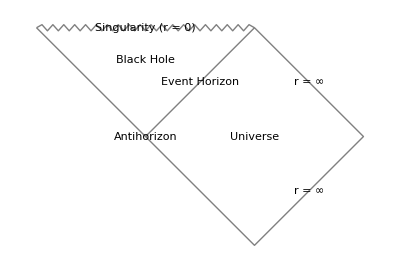

```mathematica
BlackHoleModelData["Schwarzschild","PenroseDiagram"]
```

```mathematica
BlackHoleModelData["ReissnerNordstrom","PenroseDiagram"]
```

-Graphics-

Insert values for the important physical quantities of a black hole to learn the surface gravity on the event horizon:

```mathematica
BlackHoleModelData["ReissnerNordstrom","SurfaceGravity",{"M"->10StarData["Sun", "Mass"],"Q"->Quantity[10^13, "Coulombs"]}]
```

1.52×10^12 m/s^2

Convert that to units of standard gravity:

```mathematica
UnitConvert[%,"StandardAccelerationOfGravity"]
```

1.55×10^11 g

Physical quantities can be specified as Quantity objects or numbers:

```mathematica
BlackHoleModelData["Schwarzschild","Entropy",{"M"->1}]
```

4 π k G/(ℏ c)

### Possible Issues

Quantity input is checked for the correct units:

```mathematica
BlackHoleModelData["Schwarzschild","Entropy",{"M"->Quantity[1,"Meters"]}]
```

ResourceFunction::usermessage: BlackHoleModelData

3.663×10^-7 m^4/(kg s^2 K)

Only valid physical quantities are used:

```mathematica
BlackHoleModelData["Schwarzschild","Entropy",{"O"->Quantity[1,"Meters"]}]
```

QuantityVariable::unkpq: Unknown physical quantity specification O.

(4 π k G/(ℏ c)) (M Mass)^2

Some values are not physically realizable:

```mathematica
BlackHoleModelData["KerrNewman","Temperature",{"M"->StarData["Sun", "Mass"],"J"->Quantity[10^10,"Joules""Seconds"],"Q"->Quantity[10^30,"Coulombs"]}]
```

ResourceFunction::usermessage: BlackHoleModelData

Missing[NotAvailable]

## Source & Additional Information

### Contributed By

Jason Martinez

### Keywords

black hole model data

black hole data

black hole model

black hole

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FormulaData

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Wikipedia–Black hole

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.